```mathematica
Series[Exp[-x^4 + x^3 - x^2], {x,0, 10}]
```

1-x^2+x^3-x^4/2-x^5+(4 x^6)/3-x^7/2-(11 x^8)/24+x^9-(71 x^10)/120+O[x]^11

```mathematica
Roots[x^4+3*x^3−3*x^2+10==0, x]
```

x==1/2 (-5-√5)||x==1/2 (-5+√5)||x==1-ⅈ||x==1+ⅈ

```mathematica
y[x_] = x^3*Log[x]+Cosh[x]
```

Cosh[x]+x^3 Log[x]

```mathematica
y'''[x]
```

11+6 Log[x]+Sinh[x]

```mathematica
NIntegrate[Sqrt[1-x],{x,0,1}]
```

0.666667

```mathematica
Inverse[({{1, 2, 3}, {4, 5, 8}, {3, 2, 1}})]
```

{{-11/8,1/2,1/8},{5/2,-1,1/2},{-7/8,1/2,-3/8}}

```mathematica
s = NDSolve[{f''[x] == -((Pi^2)/4)(f[x]+1), f[0]==0, f[1]==1},f,{x,0,10}]
```

{{f→InterpolatingFunction[…]}}

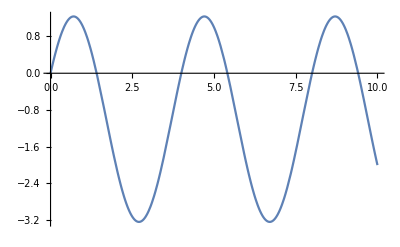

```mathematica
Plot[Evaluate[f[x]/.s],{x,0,10}]
```